# ２次曲線

2 次曲線とは2次方程式

a x^2+2 b x y+c y^2+d x+e y+f==0

を満たす点 (x, y) の集合のこと．

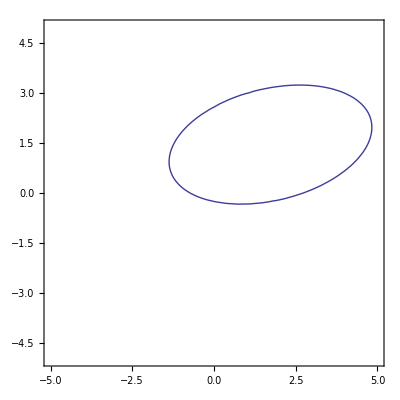

```mathematica
ContourPlot[-x^2+x*y-3y^2+2*x+7*y+2==0,{x,-5,5},{y,-5,5}]
```

## ２次曲線の種類

### （１）楕円

```mathematica
x^2/a^2+y^2/b^2==1
```

```mathematica
ContourPlot[4*x^2+y^2==1,{x,-1,1},{y,-1,1}]
```

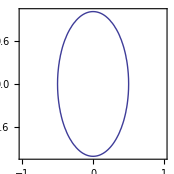

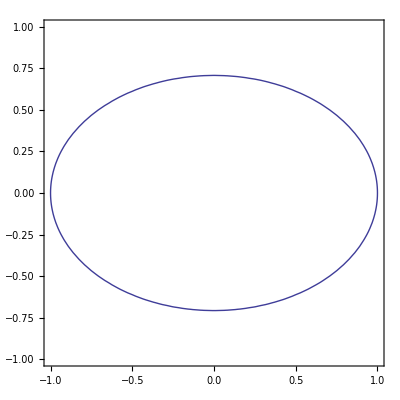

```mathematica
ContourPlot[x^2+2*y^2==1,{x,-1,1},{y,-1,1}]
```

### （２）双曲線

```mathematica
x^2/a^2-y^2/b^2==1
```

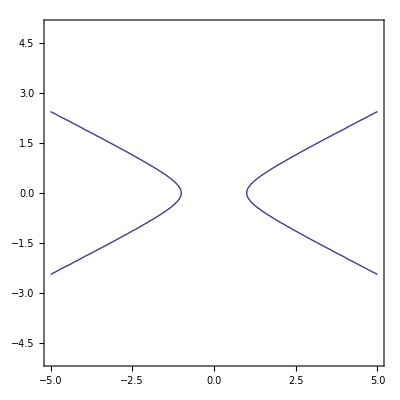

```mathematica
ContourPlot[x^2-4*y^2==1,{x,-5,5},{y,-5,5}]
```

### （３）放物線

```mathematica
y^2==4*p*x
```

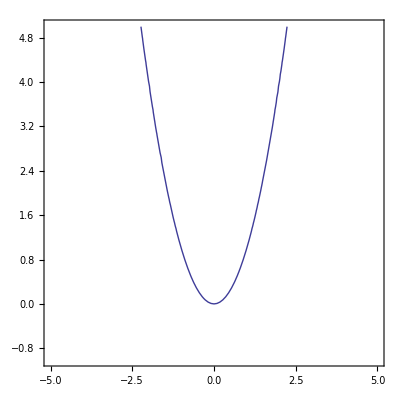

```mathematica
ContourPlot[y==x^2,{x,-5,5},{y,-1,5}]
```

### （４）２つの直線

x, y の１次式に因数分解できる場合，その2次曲線は２つの直線である．

```mathematica
Factor[2*x^2+x*y-6*y^2+7*y-2]
```

(2+2 x-3 y) (-1+x+2 y)

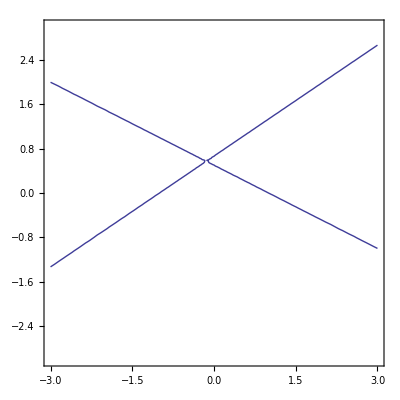

```mathematica
ContourPlot[2*x^2+x*y-6*y^2+7*y-2==0,{x,-3,3},{y,-3,3}]
```

### （５）１つの点

以下の方程式を満たす x, y は x = y = 0 のみ （Mathematica では何も描画されない）．

```mathematica
ContourPlot[x^2+y^2==0,{x,-5,5},{y,-5,5}]
```

-Graphics-

### （６）存在しない

以下の方程式を満たす実数 x, y は存在しない（Mathematica では何も描画されない）．

```mathematica
ContourPlot[x^2+y^2==-1,{x,-5,5},{y,-5,5}]
```

-Graphics-

## 目的

（４） 〜 （６） の特異な例を除けば，２次曲線は （１） 〜 （３） の種類しか存在しない．与えられた２次方程式がどの２次曲線を表すかを判定できるようになるのが目的である．